```mathematica
ClearAll["Global`*"]
```

```mathematica
ppmrfitdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ExpPred_fit_table_revreps.csv"}],"csv"];
predpreymassdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ExpPredmass_tablereps.csv"}],"csv"];
lm =LinearModelFit[Log@(predpreymassdata*1000),x,x];
lmparams=lm["BestFitParameters"];
ppmrslope = (ppmrfitdata[[3,1]]);
ppmrint = Exp[(ppmrfitdata[[2,1]])]*((1/1000)^ppmrslope)*1000; (*converted from KG to grams*)
```

```mathematica
plink[alpha_,beta_,gamma_,M_,Mp_]:=Exp[alpha+beta*Log[M/Mp]+gamma*Log[M/Mp]^2]/(1+Exp[alpha+beta*Log[M/Mp]+gamma*Log[M/Mp]^2]);
```

```mathematica
(*PredMasses = {5,45,80,250,5000,12500,35000,60000,110000};*)
(*PredMass = {63500,10000,13500,18000,79500,18000,32000,204000,81500};*)
PredMassMacro = {63500,10000,13500,18000,79500,18000,32000,204000,81500,195000}/1000;
(*PredMass = {204000,79500,81500,20000,32000,63500,195000};*)
```

```mathematica
N[PredMassMacro]
```

{63.5,10.,13.5,18.,79.5,18.,32.,204.,81.5,195.}

From serengetifit.jl 
 2.0558989052412504
 -1.918476481051926
  0.047825684997587214

```mathematica
PredMassMacro = {63500,10000,13500,18000,79500,18000,32000,204000,81500,195000}/1000;
alphamacro =2.0558989052412504;
betamacro =-1.918476481051926;
gammamacro =0.047825684997587214;
```

```mathematica
ExpectedPredMass[alpha_,beta_,gamma_,PredMass_,M_]:=(∑_(j=1)^Length[PredMass] plink[alpha,beta,gamma,M,PredMass[[j]]]*PredMass[[j]])/(∑_(j=1)^Length[PredMass] plink[alpha,beta,gamma,M,PredMass[[j]]]);
```

```mathematica
ExpectedPredMass[alphamacro,betamacro,gammamacro,PredMassMacro,400]
```

144.303

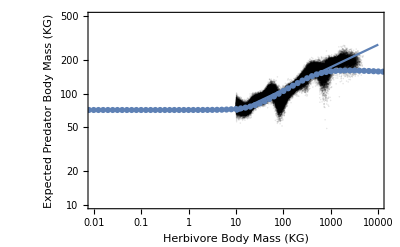

```mathematica
ExpPredMassListMacro = Table[{10^i,ExpectedPredMass[alphamacro,betamacro,gammamacro,PredMassMacro,10^i]},{i,-3,5,0.1}];
Show[{
ListLogLogPlot[predpreymassdata,Frame->True,FrameLabel->{"Herbivore Body Mass (KG)","Expected Predator Body Mass (KG)"},PlotRange->{{(10^1)/1000,(10^7)/1000},{(10^4)/1000,(5*10^5)/1000}},PlotStyle->Directive[{Opacity[0.1],Black}]],
ListLogLogPlot[ExpPredMassListMacro],
LogLogPlot[(ppmrint*M^ppmrslope)/1000/.M->(Mkg*1000),{Mkg,(10^4)/1000,(10^7)/1000}]
}]
```

Estimate visually the alpha, beta, gamma values from the Cruz/Pires paper
{alpha,gamma,beta} = {-1.5,-1,-0.12}

```mathematica
Manipulate[
Plot[Exp[alpha+beta*x+gamma*x^2]/(1+Exp[alpha+beta*x+gamma*x^2]),{x,-10,4},PlotRange->{0,1}],
{{alpha,-1.5},-3,1},{{beta,-1},-20,1},{{gamma,-0.12},-20,2}]
```

Now try the same thing, but with {alpha,gamma,beta} = {-1.5,-1,-0.12} and the set of smaller predator masses used in the Cruz/Pires Paper

```mathematica
(*PredMassMeso= {5,45,80,250,5000,12500,35000,60000,110000}/1000;*)
PredMassMeso = {51.6,100,3.249,2.2,11.9,6.949,3.9,3.59,8.99,5.23,23.2,9.83};
alphameso =-1.5;
betameso =-1;
gammameso =-0.12;

alphamesoFelids =-0.84;
betamesoFelids =-0.87;
gammamesoFelids =-0.12;

alphamesoNonFelids =-2.2;
betamesoNonFelids =-0.67;
gammamesoNonFelids =-0.02;
```

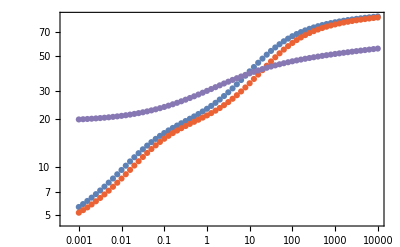

```mathematica
ExpPredMassListMeso = Table[{10^i,ExpectedPredMass[alphameso,betameso,gammameso,PredMassMeso,10^i]},{i,-3,4,0.1}];
ExpPredMassListMesoFelids = Table[{10^i,ExpectedPredMass[alphamesoFelids,betamesoFelids,gammamesoFelids,PredMassMeso,10^i]},{i,-3,4,0.1}];
ExpPredMassListMesoNonFelids = Table[{10^i,ExpectedPredMass[alphamesoNonFelids,betamesoNonFelids,gammamesoNonFelids,PredMassMeso,10^i]},{i,-3,4,0.1}];
Show[{
ListLogLogPlot[ExpPredMassListMeso,Frame->True],
ListLogLogPlot[ExpPredMassListMesoFelids,Frame->True,PlotStyle->ColorData[97,4]],
ListLogLogPlot[ExpPredMassListMesoNonFelids,Frame->True,PlotStyle->ColorData[97,5]]
}]
```

```mathematica
Mean[{220,436}]
```

328

```mathematica
ExpectedPredMass[alphamesoNonFelids,betamesoNonFelids,gammamesoNonFelids,PredMassMeso,100]
ExpectedPredMass[alphamesoFelids,betamesoFelids,gammamesoFelids,PredMassMeso,100]
```

45.9866

59.9221

```mathematica
MeanMesoNonFelidsFelids = Table[{ExpPredMassListMesoNonFelids[[i,1]],Mean[{ExpPredMassListMesoNonFelids[[i,2]],ExpPredMassListMesoFelids[[i,2]]}]},{i,1,Length[ExpPredMassListMesoFelids[[All,2]]]}];
```

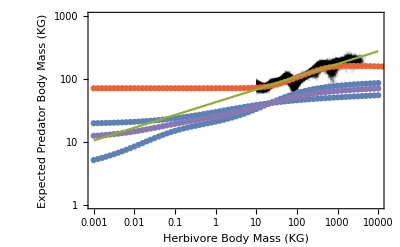

```mathematica
Show[{
ListLogLogPlot[predpreymassdata,Frame->True,FrameLabel->{"Herbivore Body Mass (KG)","Expected Predator Body Mass (KG)"},PlotRange->{{10^-3,10^4},{10^0,10^3}},PlotStyle->Directive[{Opacity[0.1],Black}]],
ListLogLogPlot[ExpPredMassListMacro,PlotStyle->ColorData[97,4]],
ListLogLogPlot[ExpPredMassListMesoFelids],
ListLogLogPlot[ExpPredMassListMesoNonFelids],
ListLogLogPlot[MeanMesoNonFelidsFelids,PlotStyle->ColorData[97,5]],
(*ListLogLogPlot[ExpPredMassListMesoFelids],
ListLogLogPlot[ExpPredMassListMesoNonFelids],*)
LogLogPlot[(ppmrint*M^ppmrslope)/1000/.M->Mkg*1000,{Mkg,10^-3,10^4},PlotStyle->ColorData[97,3]]
}]
```

NOTE - THE ABOVE CODE IS FIXED TO ASSESS EVERYTHING IN KG (WHICH IS APPROPRIATE FOR THE LOGIT PARAMS) -- BUT NOT BELOW CODE

Can we construct a general and analytical formula for Exp(predmass|preymass) assuming a lognormal predmass distribution?

```mathematica
N[Mean[Join[PredMassMeso,PredMassMacro]]]
```

42.9835

General::munfl: Exp[-7.30812×10^6] is too small to represent as a normalized machine number; precision may be lost.

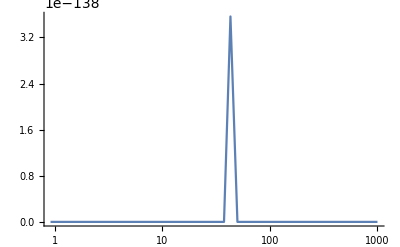

```mathematica
LogLinearPlot[PDF[LogNormalDistribution[PredMassMean,PredMassSD],Mp]/.{PredMassMean->Log[42],PredMassSD->0.001},{Mp,-3,10^3},PlotRange->All]
```

```mathematica
NIntegrate[PDF[LogNormalDistribution[PredMassMean,PredMassSD],Mp]/.{PredMassMean->Log[42],PredMassSD->0.001},{Mp,10^(-3),10^3}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
∫plink[alpha,beta,gamma,M,Mp]*((ⅇ^(-(-PredMassMean+Log[Mp])^2/(2 PredMassSD^2)))/(Mp √(2 π) PredMassSD))*MpⅆMp
```

(∫(ⅇ^(alpha+beta Log[M/Mp]+gamma Log[M/Mp]^2-(-PredMassMean+Log[Mp])^2/(2 PredMassSD^2)))/(1+ⅇ^(alpha+beta Log[M/Mp]+gamma Log[M/Mp]^2))ⅆMp)/(√(2 π) PredMassSD)

```mathematica
ExpPredMassGenForm[logitvec_,PredMassMean_,PredMassSD_,M_]:=NIntegrate[plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],M,Mp]*((ⅇ^(-(-PredMassMean+Log[Mp])^2/(2 PredMassSD^2)))/(Mp √(2 π) PredMassSD))*Mp,{Mp,1,10^6}]/NIntegrate[plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],M,Mp]*((ⅇ^(-(-PredMassMean+Log[Mp])^2/(2 PredMassSD^2)))/(Mp √(2 π) PredMassSD)),{Mp,1,10^6}];
```

```mathematica
logitmeso = {alphameso,betameso,gammameso};
logitmacro = {alphamacro,betamacro,gammamacro};
```

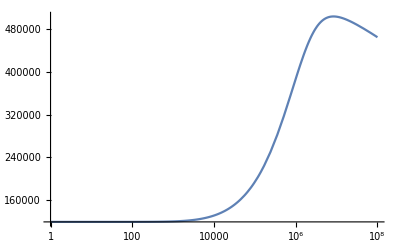

```mathematica
LogLinearPlot[ExpPredMassGenForm[logitmacro,Log[50000],1.8,M],{M,1,10^8}]
```

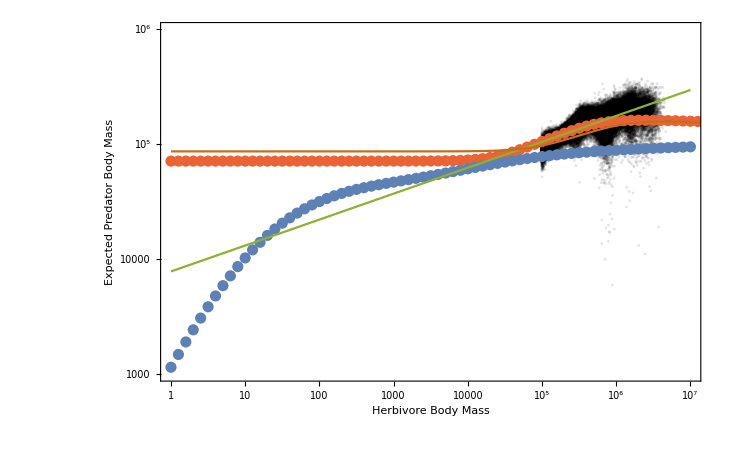

```mathematica
Show[{
ListLogLogPlot[predpreymassdata*1000,Frame->True,FrameLabel->{"Herbivore Body Mass","Expected Predator Body Mass"},PlotRange->{{10^0,10^7},{10^3,10^6}},PlotStyle->Directive[{Opacity[0.1],Black}]],
ListLogLogPlot[ExpPredMassListMacro,PlotStyle->ColorData[97,4]],
ListLogLogPlot[ExpPredMassListMeso],
(*ListLogLogPlot[ExpPredMassListMesoFelids],
ListLogLogPlot[ExpPredMassListMesoNonFelids],*)
LogLogPlot[ppmrint*M^ppmrslope,{M,10^0,10^7},PlotStyle->ColorData[97,3]],
LogLogPlot[ExpPredMassGenForm[logitmacro,Log[Mean[PredMassMacro]],(√Log[1/2 ⅇ^(-2 μ) (ⅇ^(2 μ)+√(ⅇ^(4 μ)+4 ⅇ^(2 μ) stdev^2))]/.{μ->Log[Mean[PredMassMacro]],stdev->60000}),M],{M,1,10^8},PlotStyle->ColorData[97,6]]
}
]
```

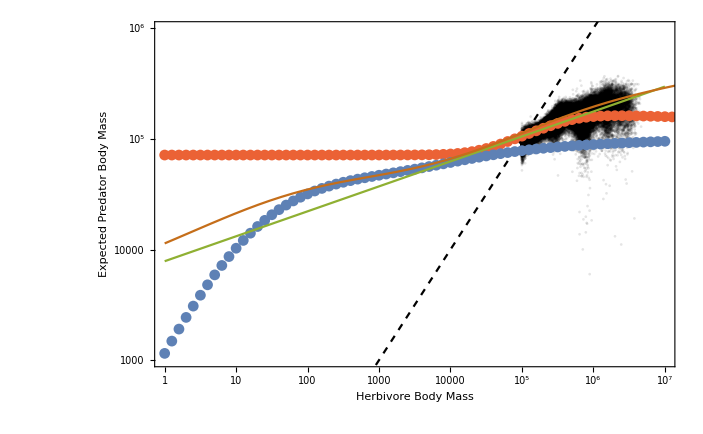

```mathematica
Show[{
ListLogLogPlot[predpreymassdata*1000,Frame->True,FrameLabel->{"Herbivore Body Mass","Expected Predator Body Mass"},PlotRange->{{10^0,10^7},{10^3,10^6}},PlotStyle->Directive[{Opacity[0.1],Black}]],
LogLogPlot[M,{M,10^0,10^7},PlotStyle->Directive[Dashed,Black]],
ListLogLogPlot[ExpPredMassListMacro,PlotStyle->ColorData[97,4]],
ListLogLogPlot[ExpPredMassListMeso],
(*ListLogLogPlot[ExpPredMassListMesoFelids],
ListLogLogPlot[ExpPredMassListMesoNonFelids],*)
LogLogPlot[ppmrint*M^ppmrslope,{M,10^0,10^7},PlotStyle->ColorData[97,3]],
LogLogPlot[ExpPredMassGenForm[logitmeso,Log[Mean[PredMassMeso]],(√Log[1/2 ⅇ^(-2 μ) (ⅇ^(2 μ)+√(ⅇ^(4 μ)+4 ⅇ^(2 μ) stdev^2))]/.{μ->Log[Mean[PredMassMeso]],stdev->70000}),M],{M,1,10^8},PlotStyle->ColorData[97,6]]
}
]
```

```mathematica
ExpPredMassGenFormSpecific[M_] := Quiet[Evaluate[ExpPredMassGenForm[logitmeso,Log[Mean[PredMassMeso]],(√Log[1/2 ⅇ^(-2 μ) (ⅇ^(2 μ)+√(ⅇ^(4 μ)+4 ⅇ^(2 μ) stdev^2))]/.{μ->Log[Mean[PredMassMeso]],stdev->70000}),M]//Simplify]];
```

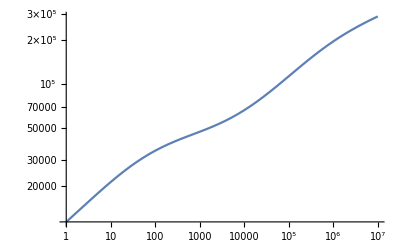

```mathematica
LogLogPlot[ExpPredMassGenFormSpecific[M],{M,1,10^7}]
```

```mathematica
(*NSolve[ppmrint*M^ppmrslope==M,M]*)
```

```mathematica
N[ppmrint^(1/(1-ppmrslope))]
```

106812.

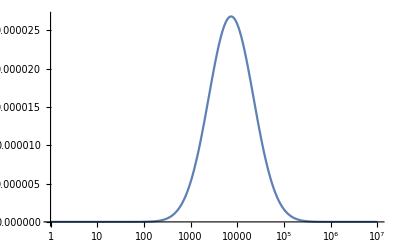

71500

72623.5

```mathematica
LogLinearPlot[PDF[LogNormalDistribution[PredMassMean,PredMassSD],Mp]/.{PredMassMean->Log[Mean[PredMassMeso]],PredMassSD->(√Log[1/2 ⅇ^(-2 μ) (ⅇ^(2 μ)+√(ⅇ^(4 μ)+4 ⅇ^(2 μ) stdev^2))]/.{μ->Log[Mean[PredMassMeso]],stdev->70000})},{Mp,1,10^7},PlotRange->All]
```

```mathematica
Mean[PredMassMacro]
N[StandardDeviation[PredMassMacro]]
N[Sqrt[ⅇ^(2 μ+σ^2) (-1+ⅇ^(σ^2))]]/.{μ->Log[Mean[PredMassMacro]],σ->0.7}
```

71500

72623.5

72639.9

```mathematica
N[StandardDeviation[PredMassMeso]]
```

38057.2

```mathematica
Solve[stdev ==Sqrt[ⅇ^(2 μ+σ^2) (-1+ⅇ^(σ^2))],σ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{σ→-√Log[1/2 ⅇ^(-2 μ) (ⅇ^(2 μ)-√(ⅇ^(4 μ)+4 ⅇ^(2 μ) stdev^2))]},{σ→√Log[1/2 ⅇ^(-2 μ) (ⅇ^(2 μ)-√(ⅇ^(4 μ)+4 ⅇ^(2 μ) stdev^2))]},{σ→-√Log[1/2 ⅇ^(-2 μ) (ⅇ^(2 μ)+√(ⅇ^(4 μ)+4 ⅇ^(2 μ) stdev^2))]},{σ→√Log[1/2 ⅇ^(-2 μ) (ⅇ^(2 μ)+√(ⅇ^(4 μ)+4 ⅇ^(2 μ) stdev^2))]}}

```mathematica
√Log[1/2 ⅇ^(-2 μ) (ⅇ^(2 μ)+√(ⅇ^(4 μ)+4 ⅇ^(2 μ) stdev^2))]/.{μ->Log[Mean[PredMassMeso]],stdev->N[StandardDeviation[PredMassMeso]]}
```

0.86577

A combined function that takes into account two sets of alpha,beta,gamma values
(note - make logitvec and means/sds a matrix, where the length determines the summation within the integrals

```mathematica
ExpPredMassGenFormCombined[logitvec1_,logitvec2_,PredMassMean1_,PredMassSD1_,PredMassMean2_,PredMassSD2_,M_]:=(NIntegrate[plink[logitvec1[[1]],logitvec1[[2]],logitvec1[[3]],M,Mp]*((ⅇ^(-(-PredMassMean1+Log[Mp])^2/(2 PredMassSD1^2)))/(Mp √(2 π) PredMassSD1))*Mp+plink[logitvec2[[1]],logitvec2[[2]],logitvec2[[3]],M,Mp]*((ⅇ^(-(-PredMassMean2+Log[Mp])^2/(2 PredMassSD2^2)))/(Mp √(2 π) PredMassSD2))*Mp,{Mp,0.1,10^6}])/(NIntegrate[plink[logitvec1[[1]],logitvec1[[2]],logitvec1[[3]],M,Mp]*((ⅇ^(-(-PredMassMean1+Log[Mp])^2/(2 PredMassSD1^2)))/(Mp √(2 π) PredMassSD1))+plink[logitvec2[[1]],logitvec2[[2]],logitvec2[[3]],M,Mp]*((ⅇ^(-(-PredMassMean2+Log[Mp])^2/(2 PredMassSD2^2)))/(Mp √(2 π) PredMassSD2)),{Mp,0.1,10^6}]);
```

```mathematica
logitvec1 = {alphameso,betameso,gammameso};
logitvec2 = {alphamacro,betamacro,gammamacro};
```

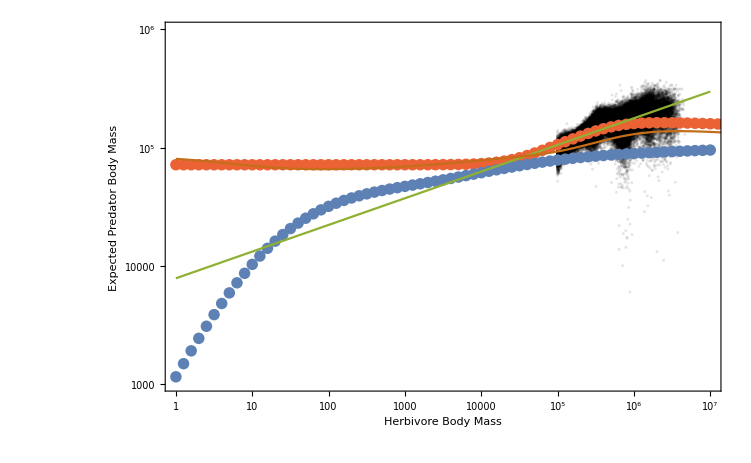

```mathematica
Show[{
ListLogLogPlot[predpreymassdata*1000,Frame->True,FrameLabel->{"Herbivore Body Mass","Expected Predator Body Mass"},PlotRange->{{10^0,10^7},{10^3,10^6}},PlotStyle->Directive[{Opacity[0.1],Black}]],
ListLogLogPlot[ExpPredMassListMacro,PlotStyle->ColorData[97,4]],
ListLogLogPlot[ExpPredMassListMeso],
(*ListLogLogPlot[ExpPredMassListMesoFelids],
ListLogLogPlot[ExpPredMassListMesoNonFelids],*)
LogLogPlot[ppmrint*M^ppmrslope,{M,10^0,10^7},PlotStyle->ColorData[97,3]],
LogLogPlot[ExpPredMassGenFormCombined[logitvec1,logitvec2,Log[Mean[PredMassMeso]],(√Log[1/2 ⅇ^(-2 μ) (ⅇ^(2 μ)+√(ⅇ^(4 μ)+4 ⅇ^(2 μ) stdev^2))]/.{μ->Log[Mean[PredMassMeso]],stdev->60000}),Log[Mean[PredMassMacro]],(√Log[1/2 ⅇ^(-2 μ) (ⅇ^(2 μ)+√(ⅇ^(4 μ)+4 ⅇ^(2 μ) stdev^2))]/.{μ->Log[Mean[PredMassMacro]],stdev->50000}),M],{M,1,10^8},PlotStyle->ColorData[97,6]]
}
]
```

```mathematica
Mean[PredMassMacro]
```

71500

```mathematica
N[Mean[PredMassMeso]]
```

24764.4

What are the raw probabilities for meso and macro across herbivore sizes? Macro line should be small for meso, and meso line should be small for macro

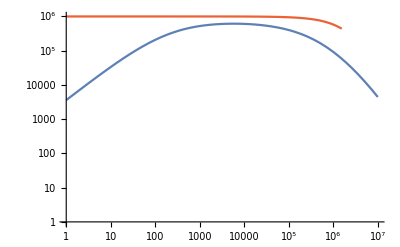

$Aborted

```mathematica
Show[{
LogLogPlot[NIntegrate[plink[logitvec1[[1]],logitvec1[[2]],logitvec1[[3]],M,Mp],{Mp,0.2,10^6}],{M,1,10^7},PlotStyle->ColorData[97,1],PlotRange->{1,10^6}],
LogLogPlot[NIntegrate[plink[logitvec2[[1]],logitvec2[[2]],logitvec2[[3]],M,Mp],{Mp,0.2,10^6}],{M,1,10^7},PlotStyle->ColorData[97,4]]
}]
```